# Visualizing Multivariable Functions in Chemistry Using Mathematica

Mathematica can aid visualization of 3D and 4D objects that are difficult for human brains, and therefore early chemistry students.

Madeleine Sutherland, Jun. 24,  2018

Several types of functions can be particularly challenging for beginning chemistry students to visualize. Hydrogen wavefunctions and probability functions are four-dimensional and students need to visualize the locations of the zero’s (nodes). For molecules, the Linear Combinations of Atomic Orbitals method involves forming molecular orbitals from linear combinations of atomic orbitals, and students must rationalize the geometric properties. In Thermochemistry, students need to visualize contour plots made from series of isotherms.

## I. Critical points of a gas, from thermochemistry

Start by explaining the basics ...

Adapted from a Physical Chemistry homework problem by Professor Andrew Berke at Smith College.

Background: Ideal gases follow the relationship PV=nRT (or PVbar=RT), but as pressure increases, molecules of gas interact more and behave non-ideally. So you have to adjust the molar volume (V/n = Vbar) for the fact that molecules take up space. A gas has totally empirical coefficients a and b for the attractive and repulsive terms respectively, in the expression van der Waals equation P = [RT/(Vbar-b)] - [a/(TVbar^2)]. In a resulting phase diagram, the critical point is where the first and second derivatives are both 0. The oscillation in the middle has little physical meaning except that you have a system with distinct phases and not a P where the two coexist. At high enough T, the substance is a gas at all P. The critical isotherm will have a phase transition of slope 0, in other words where the liquid and gas states coexist; the T value of the isotherm is Tc and the pressure at the inflection point is Pc.
Table of a and b values: https://chem.libretexts.org/Reference/Reference_Tables/Atomic_and_Molecular_Properties/A8%3A_van_der_Waal%27s_Constants_for_Real_Gases 
Plot P vs V̄ for the gas with van der Waals coefficients a = __ and b = __ via the equation P=RT/(V-b)-a/(T(V̄)^2) for 8-10 temperatures over the range __-__ K. 
i) Use the isotherms to estimate the critical temperature and pressure for this gas
ii) Would a gas with a = 2.303 have a higher or lower critical temperature? 
SiCl4: a = 20.96 L^2 bar mol^-2, b = 0.1470 L/mol
Ar: a = 1.355 L^2 bar mol^-2, b = 0.03201 L/mol, let’s have Vbar = v...

```mathematica
P[v_,t_] = (0.08314t)/(v-0.1470)-(20.96/v^2)
```

(0.08314 t)/(-0.147+v)-20.96/v^2

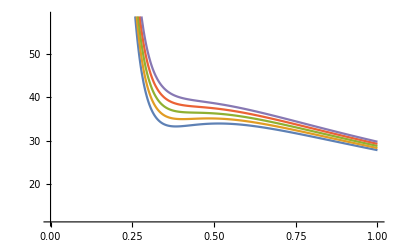

```mathematica
Plot[{P[x, 500],P[x,505],P[x,510],P[x,515],P[x,520]},{x,0,1}]
```

(0.08314 t)/(-0.03201+v)-1.355/v^2

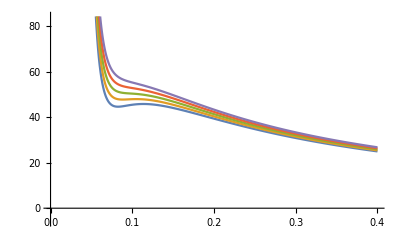

```mathematica
P'[v_,t_] = (0.08314t)/(v-0.03201)-(1.355/v^2)
Plot[{P'[x, 148],P'[x,150],P'[x,152],P'[x,154],P'[x,156]},{x,0,0.4}]
```

Notes: On the SiCl4 plot, the critical isotherm appears to be T~510K and the critical pressure around 36 bar. Indeed, the literature values: Tc = 453˚F=507K, Pc=543.8psia = 37.49 bar.
On the Ar plot, the critical isotherm appears to be T~152K, Pc~50bar. 
Indeed, the literature values: Tc=151.15K, Pc=48.7459.

## Section Header

Or show an example of application ...

Another way to start an exposition, or to expand on the basics, is to provide an example showing the application of the topic. The example might be something you arrive at by the end of the exposition, repeating that conclusion here is acceptable if it's reasonably self-contained. It might also be an example a problem scenario and the exposition explains a solution.

Always have code text as a lead-in to code that follows, to concisely indicate what it does:

```mathematica
Code (* demonstrate a specific application *)
```

## Section Header

Add more sections as needed to explain the topic....

Section names, the total number of sections, and section organization will differ based on the topic.

Here are some ideas for sections you might consider:

history/origins

derivation

applications

common misunderstandings

recent developments

unanswered questions

## Further explorations

Biochemical kinetics equations could be handled easily using sliders in Manipulate[]; that may help students “play” with the variables and see what happens when one is varied.

For physical organic chemistry, manipulating MOJ plots in Mathematica might be an easy way to explore hypotheses about the effects of changing conditions on the mechanism of the reaction in question.

## Author contact information

msuther@mit.edu

## Guidelines for the Author

### Image

Try to use images created in the Wolfram Language as much as possible

If an external image is the only way to go, use Import to get the image into the notebook and reverse close the In/Out cell-group  to hide the input cell.

### Text

Use minimal text in small pieces to explain the topic and transition between pieces of code. One or two lines of text at a time should suffice.

Sub-guideline two

### CodeText

Before each line of code, add a single line in CodeText style, as a lead-in, to say what the code that follows will do.

End this line with a colon

Make a map of Monaco:

```mathematica
GeoGraphics[Entity["Country","Monaco"]]
```

-Graphics-

### Code

Keep code simple and straightforward; code cell should be at most 3 lines long

Breakup complicated lengthy code into multiple segments and separate with CodeText lead-ins explaining each segment

Try to create simple visualizations whenever possible to illustrate the topic and add visual interest

Extra code (for example, visualization options to simply make the output look pretty) can be distracting and take away focus from the main functionality. Either avoid these or use Iconize to hide them.

Instead of

```mathematica
Plot[Sin[x], {x, 1, 10}, PlotStyle -> {Red, Dashed, Thick}]
```

Use

```mathematica
Plot[Sin[x],{x,1,10},]
```

If using a Manipulate, remember to set SaveDefinitions->True, if it refers to definitions not contained within it. This will allow the Manipulate to work without having to re-evaluate the notebook, for every new session.

Include Data Repository

Include Function Repository (mention coming soon)